# Figure 7: GPS Breeding Finite Resolution Homodyne Measurement

Here we validate our approximation, for GPS breeding, that the mixed state resulting from a homodyne measurement outcome p,  with finite resolution  2ε below a certain threshold, is well represented by the pure state resulting from an infinite resolution homodyne measurement outcome p. To do this we calculate the fidelity between the pure GPS breeding output state, ϕropt(q1|p), and the mixed GPS breeding output state ρropt (q1, q1’, ε|p) as a function of ε for n = 8 and p = 0.

The unnormalized and normalized GPS breeding output states, Φ(q|p) and φ(q|p) , are

```mathematica
f[k_,l_,γ_]:=(-1/γ^2)^(k-l)Binomial[2*k,2*l]*(2/γ)^(l+1/2)*Gamma[l+1/2];
Theta[k_,y_,γ_]:=Exp[-y^2/(2*γ)]*Sum[f[k,l,γ]*y^(2*(k-l)),{l,0,2*k}];
Φ[n_] := 1/Gamma[n+1/2]*(n/(4*Pi))^n*(Sqrt[n]/(2*Pi))*Exp[-1/2*(n*q^2)/(2*Pi)]*Sum[Theta[k,p,n/(2*Pi)]*(-1)^k*Binomial[n,k]*q^(2(n-k)),{k,0,n}];
φ[n_]:=(Exp[-1/2*(n*q^2)/(2*Pi)]*Sum[Theta[k,p,n/(2*Pi)]*(-1)^k*Binomial[n,k]*q^(2*(n-k)),{k,0,n}])/Sqrt[Sum[Theta[k,p,n/(2*Pi)]*Theta[kPrime,p,n/(2*Pi)]*(-1)^(k+kPrime)*Binomial[n,k]*Binomial[n,kPrime]*((2*Pi)/n)^(2*n-k-kPrime+1/2)Gamma[2*n-k-kPrime+1/2],{k,0,n},{kPrime,0,n}]];
```

The homodyne probability distribution is

```mathematica
HomProb[n_]:=( 1/Gamma[n+1/2]*(n/(4*Pi))^n*(Sqrt[n]/(2*Pi)))^2*Sum[Theta[k,p,n/(2*Pi)]*Theta[kPrime,p,n/(2*Pi)]*(-1)^(k+kPrime)*Binomial[n,k]*Binomial[n,kPrime]*((2*Pi)/n)^(2*n-k-kPrime+1/2)Gamma[2*n-k-kPrime+1/2],{k,0,n},{kPrime,0,n}];
```

## p = 0 Mixed State

To find the mixed state associated with a finite resolution,  2ε, homodyne measurement centered around p = 0 we first integrate Φ(q|p)*Φ*(q’|p)  from -ε to ε

```mathematica
(*Γp0 = FullSimplify[Integrate[FullSimplify[FullSimplify[Φ[8],Assumptions->{q ∈ Reals, p ∈ Reals}]*FullSimplify[Φ[8]/.q->qPrime,Assumptions->{qPrime ∈ Reals, p ∈ Reals}],Assumptions->{q ∈ Reals, qPrime ∈ Reals,p ∈ Reals}],{p,-ε,ε},Assumptions->{q ∈ Reals,qPrime ∈ Reals,ε ∈ Reals}],Assumptions->{q∈ Reals,qPrime ∈ Reals, ε ∈ Reals}];*)
Γp0 = 1/(4411822995186647040000 π^17)ⅇ^(-(2 (q^2+qPrime^2))/π) (ⅇ^(-(π ε^2)/4) π ε (-9223372036854775808 q^14 qPrime^14 (q^2+qPrime^2)+576460752303423488 π q^12 qPrime^12 (63 q^4+16 q^2 qPrime^2+63 qPrime^4)+898 π^29 ε^28-π^30 ε^30-4 π^28 ε^26 (88259+32 (q^2+qPrime^2) ε^2)+24 π^27 ε^24 (3340709+4192 (q^2+qPrime^2) ε^2)-15762598695796736 π^4 q^6 qPrime^6 (105 (q^2+qPrime^2) (279 q^8-49 q^6 qPrime^2+181 q^4 qPrime^4-49 q^2 qPrime^6+279 qPrime^8)+q^2 qPrime^2 (2975 q^8+3680 q^6 qPrime^2+4648 q^4 qPrime^4+3680 q^2 qPrime^6+2975 qPrime^8) ε^2+16 q^4 qPrime^4 (q^2+qPrime^2) (q^4+3 q^2 qPrime^2+qPrime^4) ε^4)+16 π^26 ε^22 (-730936425-2141472 (q^2+qPrime^2) ε^2-64 (7 q^4+16 q^2 qPrime^2+7 qPrime^4) ε^4)+32 π^25 ε^20 (36025886865+208193760 (q^2+qPrime^2) ε^2+64 (2415 q^4+5392 q^2 qPrime^2+2415 qPrime^4) ε^4)+985162418487296 π^5 q^4 qPrime^4 (315 (2079 q^12+2544 q^10 qPrime^2+2170 q^8 qPrime^4+1424 q^6 qPrime^6+2170 q^4 qPrime^8+2544 q^2 qPrime^10+2079 qPrime^12)+840 q^2 qPrime^2 (q^2+qPrime^2) (147 q^8+43 q^6 qPrime^2+233 q^4 qPrime^4+43 q^2 qPrime^6+147 qPrime^8) ε^2+8 q^4 qPrime^4 (245 q^8+800 q^6 qPrime^2+952 q^4 qPrime^4+800 q^2 qPrime^6+245 qPrime^8) ε^4)+128 π^23 ε^16 (29348122894335+525309593760 (q^2+qPrime^2) ε^2+192 (9825935 q^4+21186448 q^2 qPrime^2+9825935 qPrime^4) ε^4+3584 (q^2+qPrime^2) (305 q^4+851 q^2 qPrime^2+305 qPrime^4) ε^6)+246290604621824 π^6 q^2 qPrime^2 (-45 (q^2+qPrime^2) (54483 q^12+51777 q^10 qPrime^2+89931 q^8 qPrime^4+13459 q^6 qPrime^6+89931 q^4 qPrime^8+51777 q^2 qPrime^10+54483 qPrime^12)-210 q^2 qPrime^2 (4257 q^12+6672 q^10 qPrime^2+11270 q^8 qPrime^4+13936 q^6 qPrime^6+11270 q^4 qPrime^8+6672 q^2 qPrime^10+4257 qPrime^12) ε^2-336 q^4 qPrime^4 (q^2+qPrime^2) (93 q^8+197 q^6 qPrime^2+231 q^4 qPrime^4+197 q^2 qPrime^6+93 qPrime^8) ε^4-16 q^6 qPrime^6 (5 q^8+32 q^6 qPrime^2+56 q^4 qPrime^4+32 q^2 qPrime^6+5 qPrime^8) ε^6)+1924145348608 π^8 (-810 (q^2+qPrime^2) (353925 q^12+1355783 q^10 qPrime^2+1781197 q^8 qPrime^4+1043653 q^6 qPrime^6+1781197 q^4 qPrime^8+1355783 q^2 qPrime^10+353925 qPrime^12)-45 (1649505 q^16+7166016 q^14 qPrime^2+21551376 q^12 qPrime^4+42853440 q^10 qPrime^6+54414500 q^8 qPrime^8+42853440 q^6 qPrime^10+21551376 q^4 qPrime^12+7166016 q^2 qPrime^14+1649505 qPrime^16) ε^2-96 q^2 qPrime^2 (q^2+qPrime^2) (150579 q^12+517473 q^10 qPrime^2+1148331 q^8 qPrime^4+1385459 q^6 qPrime^6+1148331 q^4 qPrime^8+517473 q^2 qPrime^10+150579 qPrime^12) ε^4-192 q^4 qPrime^4 (1617 q^12+10512 q^10 qPrime^2+23590 q^8 qPrime^4+30576 q^6 qPrime^6+23590 q^4 qPrime^8+10512 q^2 qPrime^10+1617 qPrime^12) ε^6-512 q^6 qPrime^6 (q^2+qPrime^2) (q^8+9 q^6 qPrime^2+19 q^4 qPrime^4+9 q^2 qPrime^6+qPrime^8) ε^8)+34359738368 π^9 (99225 (393107 q^12+1603888 q^10 qPrime^2+2286130 q^8 qPrime^4+2052176 q^6 qPrime^6+2286130 q^4 qPrime^8+1603888 q^2 qPrime^10+393107 qPrime^12)+7560 (q^2+qPrime^2) (1293435 q^12+6222073 q^10 qPrime^2+15478067 q^8 qPrime^4+21210683 q^6 qPrime^6+15478067 q^4 qPrime^8+6222073 q^2 qPrime^10+1293435 qPrime^12) ε^2+1260 (438867 q^16+3486912 q^14 qPrime^2+12910128 q^12 qPrime^4+26351808 q^10 qPrime^6+33021100 q^8 qPrime^8+26351808 q^6 qPrime^10+12910128 q^4 qPrime^12+3486912 q^2 qPrime^14+438867 qPrime^16) ε^4+384 q^2 qPrime^2 (q^2+qPrime^2) (89661 q^12+646767 q^10 qPrime^2+1497669 q^8 qPrime^4+2044541 q^6 qPrime^6+1497669 q^4 qPrime^8+646767 q^2 qPrime^10+89661 qPrime^12) ε^6+1792 q^4 qPrime^4 (121 q^12+1296 q^10 qPrime^2+3990 q^8 qPrime^4+5488 q^6 qPrime^6+3990 q^4 qPrime^8+1296 q^2 qPrime^10+121 qPrime^12) ε^8)+8589934592 π^10 (-1091475 (q^2+qPrime^2) (311181 q^8+670709 q^6 qPrime^2+472951 q^4 qPrime^4+670709 q^2 qPrime^6+311181 qPrime^8)-66150 (1803373 q^12+10110672 q^10 qPrime^2+25310670 q^8 qPrime^4+34074544 q^6 qPrime^6+25310670 q^4 qPrime^8+10110672 q^2 qPrime^10+1803373 qPrime^12) ε^2-15120 (q^2+qPrime^2) (693121 q^12+4363931 q^10 qPrime^2+11165737 q^8 qPrime^4+14863553 q^6 qPrime^6+11165737 q^4 qPrime^8+4363931 q^2 qPrime^10+693121 qPrime^12) ε^4-120 (989703 q^16+14139840 q^14 qPrime^2+60618096 q^12 qPrime^4+134092224 q^10 qPrime^6+173141500 q^8 qPrime^8+134092224 q^6 qPrime^10+60618096 q^4 qPrime^12+14139840 q^2 qPrime^14+989703 qPrime^16) ε^6-256 q^2 qPrime^2 (q^2+qPrime^2) (10153 q^12+126291 q^10 qPrime^2+389777 q^8 qPrime^4+539753 q^6 qPrime^6+389777 q^4 qPrime^8+126291 q^2 qPrime^10+10153 qPrime^12) ε^8-3584 q^4 qPrime^4 (q^12+16 q^10 qPrime^2+70 q^8 qPrime^4+112 q^6 qPrime^6+70 q^4 qPrime^8+16 q^2 qPrime^10+qPrime^12) ε^10)+268435456 π^11 (22920975 (848315 q^8+2021344 q^6 qPrime^2+2161096 q^4 qPrime^4+2021344 q^2 qPrime^6+848315 qPrime^8)+17463600 (q^2+qPrime^2) (628433 q^8+2461017 q^6 qPrime^2+3780995 q^4 qPrime^4+2461017 q^2 qPrime^6+628433 qPrime^8) ε^2+211680 (6653075 q^12+40847664 q^10 qPrime^2+103014450 q^8 qPrime^4+137527376 q^6 qPrime^6+103014450 q^4 qPrime^8+40847664 q^2 qPrime^10+6653075 qPrime^12) ε^4+34560 (q^2+qPrime^2) (1100671 q^12+8192613 q^10 qPrime^2+22640343 q^8 qPrime^4+31235647 q^6 qPrime^6+22640343 q^4 qPrime^8+8192613 q^2 qPrime^10+1100671 qPrime^12) ε^6+1920 (50193 q^16+1162304 q^14 qPrime^2+6235152 q^12 qPrime^4+15206464 q^10 qPrime^6+20153700 q^8 qPrime^8+15206464 q^6 qPrime^10+6235152 q^4 qPrime^12+1162304 q^2 qPrime^14+50193 qPrime^16) ε^8+4096 q^2 qPrime^2 (q^2+qPrime^2) (169 q^12+3219 q^10 qPrime^2+14225 q^8 qPrime^4+21545 q^6 qPrime^6+14225 q^4 qPrime^8+3219 q^2 qPrime^10+169 qPrime^12) ε^10)+134217728 π^12 (-297972675 (q^2+qPrime^2) (182915 q^4+155529 q^2 qPrime^2+182915 qPrime^4)-7640325 (7138885 q^8+28649504 q^6 qPrime^2+43255352 q^4 qPrime^4+28649504 q^2 qPrime^6+7138885 qPrime^8) ε^2-3492720 (q^2+qPrime^2) (2799407 q^8+11350183 q^6 qPrime^2+17029245 q^4 qPrime^4+11350183 q^2 qPrime^6+2799407 qPrime^8) ε^4-30240 (13993837 q^12+92698320 q^10 qPrime^2+244705230 q^8 qPrime^4+332119984 q^6 qPrime^6+244705230 q^4 qPrime^8+92698320 q^2 qPrime^10+13993837 qPrime^12) ε^6-3840 (q^2+qPrime^2) (1013441 q^12+9424987 q^10 qPrime^2+28872041 q^8 qPrime^4+40841729 q^6 qPrime^6+28872041 q^4 qPrime^8+9424987 q^2 qPrime^10+1013441 qPrime^12) ε^8-384 (6305 q^16+217152 q^14 qPrime^2+1531152 q^12 qPrime^4+4217920 q^10 qPrime^6+5806500 q^8 qPrime^8+4217920 q^6 qPrime^10+1531152 q^4 qPrime^12+217152 q^2 qPrime^14+6305 qPrime^16) ε^10-4096 q^2 qPrime^2 (q^2+qPrime^2) (q^12+27 q^10 qPrime^2+169 q^8 qPrime^4+321 q^6 qPrime^6+169 q^4 qPrime^8+27 q^2 qPrime^10+qPrime^12) ε^12)+8388608 π^13 (127702575 (7222845 q^4+10742192 q^2 qPrime^2+7222845 qPrime^4)+794593800 (q^2+qPrime^2) (2213245 q^4+4477047 q^2 qPrime^2+2213245 qPrime^4) ε^2+12224520 (36125115 q^8+145151968 q^6 qPrime^2+217889224 q^4 qPrime^4+145151968 q^2 qPrime^6+36125115 qPrime^8) ε^4+27941760 (q^2+qPrime^2) (1019239 q^8+4380831 q^6 qPrime^2+6725285 q^4 qPrime^4+4380831 q^2 qPrime^6+1019239 qPrime^8) ε^6+26880 (18422547 q^12+134857008 q^10 qPrime^2+374153010 q^8 qPrime^4+515352656 q^6 qPrime^6+374153010 q^4 qPrime^8+134857008 q^2 qPrime^10+18422547 qPrime^12) ε^8+6144 (q^2+qPrime^2) (252785 q^12+3074539 q^10 qPrime^2+10658201 q^8 qPrime^4+15676849 q^6 qPrime^6+10658201 q^4 qPrime^8+3074539 q^2 qPrime^10+252785 qPrime^12) ε^10+1024 (225 q^16+10816 q^14 qPrime^2+101136 q^12 qPrime^4+329280 q^10 qPrime^6+475300 q^8 qPrime^8+329280 q^6 qPrime^10+101136 q^4 qPrime^12+10816 q^2 qPrime^14+225 qPrime^16) ε^12)+2097152 π^14 (-2785593508322625 (q^2+qPrime^2)-255405150 (41747265 q^4+83887984 q^2 qPrime^2+41747265 qPrime^4) ε^2-1589187600 (q^2+qPrime^2) (2469607 q^4+4951221 q^2 qPrime^2+2469607 qPrime^4) ε^4-3492720 (106978885 q^8+442705952 q^6 qPrime^2+671516216 q^4 qPrime^4+442705952 q^2 qPrime^6+106978885 qPrime^8) ε^6-6209280 (q^2+qPrime^2) (1693081 q^8+7783009 q^6 qPrime^2+12184155 q^4 qPrime^4+7783009 q^2 qPrime^6+1693081 qPrime^8) ε^8-53760 (1435239 q^12+11781744 q^10 qPrime^2+34664490 q^8 qPrime^4+48639248 q^6 qPrime^6+34664490 q^4 qPrime^8+11781744 q^2 qPrime^10+1435239 qPrime^12) ε^10-12288 (q^2+qPrime^2) (6315 q^12+101513 q^10 qPrime^2+414947 q^8 qPrime^4+641003 q^6 qPrime^6+414947 q^4 qPrime^8+101513 q^2 qPrime^10+6315 qPrime^12) ε^12-2048 (q^16+64 q^14 qPrime^2+784 q^12 qPrime^4+3136 q^10 qPrime^6+4900 q^8 qPrime^8+3136 q^6 qPrime^10+784 q^4 qPrime^12+64 q^2 qPrime^14+qPrime^16) ε^14)-144115188075855872 π^2 q^10 qPrime^10 (735 qPrime^6+14 q^2 qPrime^4 (18+qPrime^2 ε^2)+7 q^6 (105+2 qPrime^2 ε^2)+4 q^4 qPrime^2 (63+8 qPrime^2 ε^2))+31525197391593472 π^3 q^8 qPrime^8 (7875 qPrime^8+288 q^6 qPrime^2 (15+2 qPrime^2 ε^2)+80 q^2 qPrime^6 (54+5 qPrime^2 ε^2)+25 q^8 (315+16 qPrime^2 ε^2)+24 q^4 qPrime^4 (91+24 qPrime^2 ε^2))+64 π^24 ε^18 (-1229991326235+32 ε^2 (-400750575 (q^2+qPrime^2)-6 (118615 q^4+259856 q^2 qPrime^2+118615 qPrime^4) ε^2-112 (q^2+qPrime^2) (q^4+3 q^2 qPrime^2+qPrime^4) ε^4))+1792 π^22 ε^14 (-69696694162215+32 ε^2 (-65271569175 (q^2+qPrime^2)-90 (4826829 q^4+10266800 q^2 qPrime^2+4826829 qPrime^4) ε^2-16 (q^2+qPrime^2) (38945 q^4+102371 q^2 qPrime^2+38945 qPrime^4) ε^4-16 (5 q^8+32 q^6 qPrime^2+56 q^4 qPrime^4+32 q^2 qPrime^6+5 qPrime^8) ε^6))+3584 π^21 ε^12 (795956734574775+32 ε^2 (1239895105785 (q^2+qPrime^2)+810 (18026113 q^4+37890928 q^2 qPrime^2+18026113 qPrime^4) ε^2+1680 (q^2+qPrime^2) (26083 q^4+65193 q^2 qPrime^2+26083 qPrime^4) ε^4+16 (1365 q^8+7968 q^6 qPrime^2+13496 q^4 qPrime^4+7968 q^2 qPrime^6+1365 qPrime^8) ε^6))+7168 π^20 ε^10 (-6083079901075125+32 ε^2 (-15927957419625 (q^2+qPrime^2)-270 (1205124109 q^4+2506941616 q^2 qPrime^2+1205124109 qPrime^4) ε^2-1680 (q^2+qPrime^2) (1116503 q^4+2672133 q^2 qPrime^2+1116503 qPrime^4) ε^4-336 (7235 q^8+39136 q^6 qPrime^2+64648 q^4 qPrime^4+39136 q^2 qPrime^6+7235 qPrime^8) ε^6-256 (q^2+qPrime^2) (q^8+9 q^6 qPrime^2+19 q^4 qPrime^4+9 q^2 qPrime^6+qPrime^8) ε^8))+14336 π^19 ε^8 (29826127266989625+32 ε^2 (135239000431275 (q^2+qPrime^2)+270 (17779660605 q^4+36645099952 q^2 qPrime^2+17779660605 qPrime^4) ε^2+1680 (q^2+qPrime^2) (30336281 q^4+69904203 q^2 qPrime^2+30336281 qPrime^4) ε^4+336 (431335 q^8+2190176 q^6 qPrime^2+3544808 q^4 qPrime^4+2190176 q^2 qPrime^6+431335 qPrime^8) ε^6+256 (q^2+qPrime^2) (249 q^8+1921 q^6 qPrime^2+3707 q^4 qPrime^4+1921 q^2 qPrime^6+249 qPrime^8) ε^8))+28672 π^18 ε^6 (-87821681475045375+32 ε^2 (-729329470187175 (q^2+qPrime^2)-10530 (4373656385 q^4+8940095344 q^2 qPrime^2+4373656385 qPrime^4) ε^2-5040 (q^2+qPrime^2) (176465795 q^4+393234057 q^2 qPrime^2+176465795 qPrime^4) ε^4-336 (15188505 q^8+73105568 q^6 qPrime^2+116322584 q^4 qPrime^4+73105568 q^2 qPrime^6+15188505 qPrime^8) ε^6-768 (q^2+qPrime^2) (8163 q^8+54907 q^6 qPrime^2+99289 q^4 qPrime^4+54907 q^2 qPrime^6+8163 qPrime^8) ε^8-512 (q^12+16 q^10 qPrime^2+70 q^8 qPrime^4+112 q^6 qPrime^6+70 q^4 qPrime^8+16 q^2 qPrime^10+qPrime^12) ε^10))+57344 π^17 ε^4 (139221886078650375+32 ε^2 (2342455440264225 (q^2+qPrime^2)+579150 (478379251 q^4+970525520 q^2 qPrime^2+478379251 qPrime^4) ε^2+65520 (q^2+qPrime^2) (150633085 q^4+325799799 q^2 qPrime^2+150633085 qPrime^4) ε^4+5040 (21858535 q^8+100499296 q^6 qPrime^2+157595368 q^4 qPrime^4+100499296 q^2 qPrime^6+21858535 qPrime^8) ε^6+768 (q^2+qPrime^2) (414389 q^8+2477661 q^6 qPrime^2+4265327 q^4 qPrime^4+2477661 q^2 qPrime^6+414389 qPrime^8) ε^8+512 (233 q^12+3088 q^10 qPrime^2+11830 q^8 qPrime^4+18032 q^6 qPrime^6+11830 q^4 qPrime^8+3088 q^2 qPrime^10+233 qPrime^12) ε^10))+16384 π^16 ε^2 (-692277641657476875+32 ε^2 (-28160522453638575 (q^2+qPrime^2)-12162150 (565314855 q^4+1139318288 q^2 qPrime^2+565314855 qPrime^4) ε^2-25225200 (q^2+qPrime^2) (18734311 q^4+39442101 q^2 qPrime^2+18734311 qPrime^4) ε^4-35280 (290434885 q^8+1283278880 q^6 qPrime^2+1987173944 q^4 qPrime^4+1283278880 q^2 qPrime^6+290434885 qPrime^8) ε^6-188160 (q^2+qPrime^2) (340599 q^8+1841711 q^6 qPrime^2+3050197 q^4 qPrime^4+1841711 q^2 qPrime^6+340599 qPrime^8) ε^8-3584 (20771 q^12+229936 q^10 qPrime^2+790930 q^8 qPrime^4+1165136 q^6 qPrime^6+790930 q^4 qPrime^8+229936 q^2 qPrime^10+20771 qPrime^12) ε^10-4096 (q^2+qPrime^2) (q^12+27 q^10 qPrime^2+169 q^8 qPrime^4+321 q^6 qPrime^6+169 q^4 qPrime^8+27 q^2 qPrime^10+qPrime^12) ε^12))+32768 π^15 (77377521896049375+32 ε^2 (21511160985439125 (q^2+qPrime^2)+255405150 (50628851 q^4+101305168 q^2 qPrime^2+50628851 qPrime^4) ε^2+227026800 (q^2+qPrime^2) (8276249 q^4+17013579 q^2 qPrime^2+8276249 qPrime^4) ε^4+388080 (211094715 q^8+900741088 q^6 qPrime^2+1379320264 q^4 qPrime^4+900741088 q^2 qPrime^6+211094715 qPrime^8) ε^6+564480 (q^2+qPrime^2) (1909479 q^8+9464351 q^6 qPrime^2+15200037 q^4 qPrime^4+9464351 q^2 qPrime^6+1909479 qPrime^8) ε^8+53760 (60957 q^12+573904 q^10 qPrime^2+1811950 q^8 qPrime^4+2598064 q^6 qPrime^6+1811950 q^4 qPrime^8+573904 q^2 qPrime^10+60957 qPrime^12) ε^10+4096 (q^2+qPrime^2) (225 q^12+4731 q^10 qPrime^2+23689 q^8 qPrime^4+39521 q^6 qPrime^6+23689 q^4 qPrime^8+4731 q^2 qPrime^10+225 qPrime^12) ε^12))+3848290697216 π^7 (73841625 qPrime^16+617760 q^2 qPrime^14 (482+107 qPrime^2 ε^2)+576 q^6 qPrime^10 (1245825+540470 qPrime^2 ε^2+29232 qPrime^4 ε^4+72 qPrime^6 ε^6)+980 q^8 qPrime^8 (568125+486960 qPrime^2 ε^2+32160 qPrime^4 ε^4+256 qPrime^6 ε^6)+1344 q^10 qPrime^6 (533925+355075 qPrime^2 ε^2+28304 qPrime^4 ε^4+352 qPrime^6 ε^6)+336 q^12 qPrime^4 (1985445+926520 qPrime^2 ε^2+93800 qPrime^4 ε^4+1408 qPrime^6 ε^6)+64 q^14 qPrime^2 (4652505+2307690 qPrime^2 ε^2+263088 qPrime^4 ε^4+3920 qPrime^6 ε^6)+33264 q^4 qPrime^12 (20055+148 qPrime^2 ε^2 (30+qPrime^2 ε^2))+27 q^16 (2734875+32 qPrime^2 ε^2 (76505+5698 qPrime^2 ε^2+48 qPrime^4 ε^4))))+32768 (191898783962510625 π^16+281474976710656 q^16 qPrime^16-396178134632280000 π^15 (q^2+qPrime^2)-281474976710656 π q^14 qPrime^14 (q^2+qPrime^2)-226676633863680000 π^13 (q^2+qPrime^2) (q^4+3 q^2 qPrime^2+qPrime^4)-461794883665920 π^3 q^10 qPrime^10 (q^2+qPrime^2) (q^4+3 q^2 qPrime^2+qPrime^4)+54645259949280000 π^14 (7 q^4+16 q^2 qPrime^2+7 qPrime^4)+52776558133248 π^2 q^12 qPrime^12 (7 q^4+16 q^2 qPrime^2+7 qPrime^4)-25230094899609600 π^11 (q^2+qPrime^2) (q^8+9 q^6 qPrime^2+19 q^4 qPrime^4+9 q^2 qPrime^6+qPrime^8)-454579338608640 π^5 q^6 qPrime^6 (q^2+qPrime^2) (q^8+9 q^6 qPrime^2+19 q^4 qPrime^4+9 q^2 qPrime^6+qPrime^8)+18134130709094400 π^12 (5 q^8+32 q^6 qPrime^2+56 q^4 qPrime^4+32 q^2 qPrime^6+5 qPrime^8)+101017630801920 π^4 q^8 qPrime^8 (5 q^8+32 q^6 qPrime^2+56 q^4 qPrime^4+32 q^2 qPrime^6+5 qPrime^8)+4805732361830400 π^10 (q^12+16 q^10 qPrime^2+70 q^8 qPrime^4+112 q^6 qPrime^6+70 q^4 qPrime^8+16 q^2 qPrime^10+qPrime^12)+312523295293440 π^6 q^4 qPrime^4 (q^12+16 q^10 qPrime^2+70 q^8 qPrime^4+112 q^6 qPrime^6+70 q^4 qPrime^8+16 q^2 qPrime^10+qPrime^12)-578133216460800 π^9 (q^2+qPrime^2) (q^12+27 q^10 qPrime^2+169 q^8 qPrime^4+321 q^6 qPrime^6+169 q^4 qPrime^8+27 q^2 qPrime^10+qPrime^12)-145100101386240 π^7 q^2 qPrime^2 (q^2+qPrime^2) (q^12+27 q^10 qPrime^2+169 q^8 qPrime^4+321 q^6 qPrime^6+169 q^4 qPrime^8+27 q^2 qPrime^10+qPrime^12)+34007836262400 π^8 (q^16+64 q^14 qPrime^2+784 q^12 qPrime^4+3136 q^10 qPrime^6+4900 q^8 qPrime^8+3136 q^6 qPrime^10+784 q^4 qPrime^12+64 q^2 qPrime^14+qPrime^16)) Erf[(√π ε)/2]);
```

The probability of obtaining a measurement outcome between  -ε to ε, Pp0ε, is the normalization constant of Γp0 and is found by integrating Γp0 over all phase space

```mathematica
(*TildePp0ε = FullSimplify[Integrate[Γp0/.qPrime->q,{q,-∞,∞},Assumptions->{ε >0}],Assumptions->{ε >0}];*)
TildePp0ε = -1/8823645990373294080000 ⅇ^(-(π ε^2)/4) ε (-388084848599243980800+π ε^2 (8123524382097937612800+π ε^2 (-5747579620158871756800+π ε^2 (1847759744219700326400+π ε^2 (-319778822996820633600+π ε^2 (33264530134663726080+π ε^2 (-2221930517648647680+π ε^2 (99417422844875520+π ε^2 (-3059227004400000+π ε^2 (65665530302400+π ε^2 (-986379808416+π ε^2 (10279540176+π ε^2 (-72525240+π ε^2 (329324+π ε^2 (-866+π ε^2)))))))))))))))+Erf[(√π ε)/2];
```

The normalized mixed state is then the unnormalized state divided by the probability

```mathematica
(*ρp0 =Simplify[Γp0/Pp0,Assumptions->{q∈ Reals,qPrime ∈ Reals, ε ∈ Reals}];*)
ρp0 = (ⅇ^(-(2 (q^2+qPrime^2))/π) (ⅇ^(-(π ε^2)/4) π ε (-9223372036854775808 q^14 qPrime^14 (q^2+qPrime^2)+576460752303423488 π q^12 qPrime^12 (63 q^4+16 q^2 qPrime^2+63 qPrime^4)+898 π^29 ε^28-π^30 ε^30-4 π^28 ε^26 (88259+32 (q^2+qPrime^2) ε^2)+24 π^27 ε^24 (3340709+4192 (q^2+qPrime^2) ε^2)-15762598695796736 π^4 q^6 qPrime^6 (105 (q^2+qPrime^2) (279 q^8-49 q^6 qPrime^2+181 q^4 qPrime^4-49 q^2 qPrime^6+279 qPrime^8)+q^2 qPrime^2 (2975 q^8+3680 q^6 qPrime^2+4648 q^4 qPrime^4+3680 q^2 qPrime^6+2975 qPrime^8) ε^2+16 q^4 qPrime^4 (q^2+qPrime^2) (q^4+3 q^2 qPrime^2+qPrime^4) ε^4)+16 π^26 ε^22 (-730936425-2141472 (q^2+qPrime^2) ε^2-64 (7 q^4+16 q^2 qPrime^2+7 qPrime^4) ε^4)+32 π^25 ε^20 (36025886865+208193760 (q^2+qPrime^2) ε^2+64 (2415 q^4+5392 q^2 qPrime^2+2415 qPrime^4) ε^4)+985162418487296 π^5 q^4 qPrime^4 (315 (2079 q^12+2544 q^10 qPrime^2+2170 q^8 qPrime^4+1424 q^6 qPrime^6+2170 q^4 qPrime^8+2544 q^2 qPrime^10+2079 qPrime^12)+840 q^2 qPrime^2 (q^2+qPrime^2) (147 q^8+43 q^6 qPrime^2+233 q^4 qPrime^4+43 q^2 qPrime^6+147 qPrime^8) ε^2+8 q^4 qPrime^4 (245 q^8+800 q^6 qPrime^2+952 q^4 qPrime^4+800 q^2 qPrime^6+245 qPrime^8) ε^4)+128 π^23 ε^16 (29348122894335+525309593760 (q^2+qPrime^2) ε^2+192 (9825935 q^4+21186448 q^2 qPrime^2+9825935 qPrime^4) ε^4+3584 (q^2+qPrime^2) (305 q^4+851 q^2 qPrime^2+305 qPrime^4) ε^6)+246290604621824 π^6 q^2 qPrime^2 (-45 (q^2+qPrime^2) (54483 q^12+51777 q^10 qPrime^2+89931 q^8 qPrime^4+13459 q^6 qPrime^6+89931 q^4 qPrime^8+51777 q^2 qPrime^10+54483 qPrime^12)-210 q^2 qPrime^2 (4257 q^12+6672 q^10 qPrime^2+11270 q^8 qPrime^4+13936 q^6 qPrime^6+11270 q^4 qPrime^8+6672 q^2 qPrime^10+4257 qPrime^12) ε^2-336 q^4 qPrime^4 (q^2+qPrime^2) (93 q^8+197 q^6 qPrime^2+231 q^4 qPrime^4+197 q^2 qPrime^6+93 qPrime^8) ε^4-16 q^6 qPrime^6 (5 q^8+32 q^6 qPrime^2+56 q^4 qPrime^4+32 q^2 qPrime^6+5 qPrime^8) ε^6)+1924145348608 π^8 (-810 (q^2+qPrime^2) (353925 q^12+1355783 q^10 qPrime^2+1781197 q^8 qPrime^4+1043653 q^6 qPrime^6+1781197 q^4 qPrime^8+1355783 q^2 qPrime^10+353925 qPrime^12)-45 (1649505 q^16+7166016 q^14 qPrime^2+21551376 q^12 qPrime^4+42853440 q^10 qPrime^6+54414500 q^8 qPrime^8+42853440 q^6 qPrime^10+21551376 q^4 qPrime^12+7166016 q^2 qPrime^14+1649505 qPrime^16) ε^2-96 q^2 qPrime^2 (q^2+qPrime^2) (150579 q^12+517473 q^10 qPrime^2+1148331 q^8 qPrime^4+1385459 q^6 qPrime^6+1148331 q^4 qPrime^8+517473 q^2 qPrime^10+150579 qPrime^12) ε^4-192 q^4 qPrime^4 (1617 q^12+10512 q^10 qPrime^2+23590 q^8 qPrime^4+30576 q^6 qPrime^6+23590 q^4 qPrime^8+10512 q^2 qPrime^10+1617 qPrime^12) ε^6-512 q^6 qPrime^6 (q^2+qPrime^2) (q^8+9 q^6 qPrime^2+19 q^4 qPrime^4+9 q^2 qPrime^6+qPrime^8) ε^8)+34359738368 π^9 (99225 (393107 q^12+1603888 q^10 qPrime^2+2286130 q^8 qPrime^4+2052176 q^6 qPrime^6+2286130 q^4 qPrime^8+1603888 q^2 qPrime^10+393107 qPrime^12)+7560 (q^2+qPrime^2) (1293435 q^12+6222073 q^10 qPrime^2+15478067 q^8 qPrime^4+21210683 q^6 qPrime^6+15478067 q^4 qPrime^8+6222073 q^2 qPrime^10+1293435 qPrime^12) ε^2+1260 (438867 q^16+3486912 q^14 qPrime^2+12910128 q^12 qPrime^4+26351808 q^10 qPrime^6+33021100 q^8 qPrime^8+26351808 q^6 qPrime^10+12910128 q^4 qPrime^12+3486912 q^2 qPrime^14+438867 qPrime^16) ε^4+384 q^2 qPrime^2 (q^2+qPrime^2) (89661 q^12+646767 q^10 qPrime^2+1497669 q^8 qPrime^4+2044541 q^6 qPrime^6+1497669 q^4 qPrime^8+646767 q^2 qPrime^10+89661 qPrime^12) ε^6+1792 q^4 qPrime^4 (121 q^12+1296 q^10 qPrime^2+3990 q^8 qPrime^4+5488 q^6 qPrime^6+3990 q^4 qPrime^8+1296 q^2 qPrime^10+121 qPrime^12) ε^8)+8589934592 π^10 (-1091475 (q^2+qPrime^2) (311181 q^8+670709 q^6 qPrime^2+472951 q^4 qPrime^4+670709 q^2 qPrime^6+311181 qPrime^8)-66150 (1803373 q^12+10110672 q^10 qPrime^2+25310670 q^8 qPrime^4+34074544 q^6 qPrime^6+25310670 q^4 qPrime^8+10110672 q^2 qPrime^10+1803373 qPrime^12) ε^2-15120 (q^2+qPrime^2) (693121 q^12+4363931 q^10 qPrime^2+11165737 q^8 qPrime^4+14863553 q^6 qPrime^6+11165737 q^4 qPrime^8+4363931 q^2 qPrime^10+693121 qPrime^12) ε^4-120 (989703 q^16+14139840 q^14 qPrime^2+60618096 q^12 qPrime^4+134092224 q^10 qPrime^6+173141500 q^8 qPrime^8+134092224 q^6 qPrime^10+60618096 q^4 qPrime^12+14139840 q^2 qPrime^14+989703 qPrime^16) ε^6-256 q^2 qPrime^2 (q^2+qPrime^2) (10153 q^12+126291 q^10 qPrime^2+389777 q^8 qPrime^4+539753 q^6 qPrime^6+389777 q^4 qPrime^8+126291 q^2 qPrime^10+10153 qPrime^12) ε^8-3584 q^4 qPrime^4 (q^12+16 q^10 qPrime^2+70 q^8 qPrime^4+112 q^6 qPrime^6+70 q^4 qPrime^8+16 q^2 qPrime^10+qPrime^12) ε^10)+268435456 π^11 (22920975 (848315 q^8+2021344 q^6 qPrime^2+2161096 q^4 qPrime^4+2021344 q^2 qPrime^6+848315 qPrime^8)+17463600 (q^2+qPrime^2) (628433 q^8+2461017 q^6 qPrime^2+3780995 q^4 qPrime^4+2461017 q^2 qPrime^6+628433 qPrime^8) ε^2+211680 (6653075 q^12+40847664 q^10 qPrime^2+103014450 q^8 qPrime^4+137527376 q^6 qPrime^6+103014450 q^4 qPrime^8+40847664 q^2 qPrime^10+6653075 qPrime^12) ε^4+34560 (q^2+qPrime^2) (1100671 q^12+8192613 q^10 qPrime^2+22640343 q^8 qPrime^4+31235647 q^6 qPrime^6+22640343 q^4 qPrime^8+8192613 q^2 qPrime^10+1100671 qPrime^12) ε^6+1920 (50193 q^16+1162304 q^14 qPrime^2+6235152 q^12 qPrime^4+15206464 q^10 qPrime^6+20153700 q^8 qPrime^8+15206464 q^6 qPrime^10+6235152 q^4 qPrime^12+1162304 q^2 qPrime^14+50193 qPrime^16) ε^8+4096 q^2 qPrime^2 (q^2+qPrime^2) (169 q^12+3219 q^10 qPrime^2+14225 q^8 qPrime^4+21545 q^6 qPrime^6+14225 q^4 qPrime^8+3219 q^2 qPrime^10+169 qPrime^12) ε^10)+134217728 π^12 (-297972675 (q^2+qPrime^2) (182915 q^4+155529 q^2 qPrime^2+182915 qPrime^4)-7640325 (7138885 q^8+28649504 q^6 qPrime^2+43255352 q^4 qPrime^4+28649504 q^2 qPrime^6+7138885 qPrime^8) ε^2-3492720 (q^2+qPrime^2) (2799407 q^8+11350183 q^6 qPrime^2+17029245 q^4 qPrime^4+11350183 q^2 qPrime^6+2799407 qPrime^8) ε^4-30240 (13993837 q^12+92698320 q^10 qPrime^2+244705230 q^8 qPrime^4+332119984 q^6 qPrime^6+244705230 q^4 qPrime^8+92698320 q^2 qPrime^10+13993837 qPrime^12) ε^6-3840 (q^2+qPrime^2) (1013441 q^12+9424987 q^10 qPrime^2+28872041 q^8 qPrime^4+40841729 q^6 qPrime^6+28872041 q^4 qPrime^8+9424987 q^2 qPrime^10+1013441 qPrime^12) ε^8-384 (6305 q^16+217152 q^14 qPrime^2+1531152 q^12 qPrime^4+4217920 q^10 qPrime^6+5806500 q^8 qPrime^8+4217920 q^6 qPrime^10+1531152 q^4 qPrime^12+217152 q^2 qPrime^14+6305 qPrime^16) ε^10-4096 q^2 qPrime^2 (q^2+qPrime^2) (q^12+27 q^10 qPrime^2+169 q^8 qPrime^4+321 q^6 qPrime^6+169 q^4 qPrime^8+27 q^2 qPrime^10+qPrime^12) ε^12)+8388608 π^13 (127702575 (7222845 q^4+10742192 q^2 qPrime^2+7222845 qPrime^4)+794593800 (q^2+qPrime^2) (2213245 q^4+4477047 q^2 qPrime^2+2213245 qPrime^4) ε^2+12224520 (36125115 q^8+145151968 q^6 qPrime^2+217889224 q^4 qPrime^4+145151968 q^2 qPrime^6+36125115 qPrime^8) ε^4+27941760 (q^2+qPrime^2) (1019239 q^8+4380831 q^6 qPrime^2+6725285 q^4 qPrime^4+4380831 q^2 qPrime^6+1019239 qPrime^8) ε^6+26880 (18422547 q^12+134857008 q^10 qPrime^2+374153010 q^8 qPrime^4+515352656 q^6 qPrime^6+374153010 q^4 qPrime^8+134857008 q^2 qPrime^10+18422547 qPrime^12) ε^8+6144 (q^2+qPrime^2) (252785 q^12+3074539 q^10 qPrime^2+10658201 q^8 qPrime^4+15676849 q^6 qPrime^6+10658201 q^4 qPrime^8+3074539 q^2 qPrime^10+252785 qPrime^12) ε^10+1024 (225 q^16+10816 q^14 qPrime^2+101136 q^12 qPrime^4+329280 q^10 qPrime^6+475300 q^8 qPrime^8+329280 q^6 qPrime^10+101136 q^4 qPrime^12+10816 q^2 qPrime^14+225 qPrime^16) ε^12)+2097152 π^14 (-2785593508322625 (q^2+qPrime^2)-255405150 (41747265 q^4+83887984 q^2 qPrime^2+41747265 qPrime^4) ε^2-1589187600 (q^2+qPrime^2) (2469607 q^4+4951221 q^2 qPrime^2+2469607 qPrime^4) ε^4-3492720 (106978885 q^8+442705952 q^6 qPrime^2+671516216 q^4 qPrime^4+442705952 q^2 qPrime^6+106978885 qPrime^8) ε^6-6209280 (q^2+qPrime^2) (1693081 q^8+7783009 q^6 qPrime^2+12184155 q^4 qPrime^4+7783009 q^2 qPrime^6+1693081 qPrime^8) ε^8-53760 (1435239 q^12+11781744 q^10 qPrime^2+34664490 q^8 qPrime^4+48639248 q^6 qPrime^6+34664490 q^4 qPrime^8+11781744 q^2 qPrime^10+1435239 qPrime^12) ε^10-12288 (q^2+qPrime^2) (6315 q^12+101513 q^10 qPrime^2+414947 q^8 qPrime^4+641003 q^6 qPrime^6+414947 q^4 qPrime^8+101513 q^2 qPrime^10+6315 qPrime^12) ε^12-2048 (q^16+64 q^14 qPrime^2+784 q^12 qPrime^4+3136 q^10 qPrime^6+4900 q^8 qPrime^8+3136 q^6 qPrime^10+784 q^4 qPrime^12+64 q^2 qPrime^14+qPrime^16) ε^14)-144115188075855872 π^2 q^10 qPrime^10 (735 qPrime^6+14 q^2 qPrime^4 (18+qPrime^2 ε^2)+7 q^6 (105+2 qPrime^2 ε^2)+4 q^4 qPrime^2 (63+8 qPrime^2 ε^2))+31525197391593472 π^3 q^8 qPrime^8 (7875 qPrime^8+288 q^6 qPrime^2 (15+2 qPrime^2 ε^2)+80 q^2 qPrime^6 (54+5 qPrime^2 ε^2)+25 q^8 (315+16 qPrime^2 ε^2)+24 q^4 qPrime^4 (91+24 qPrime^2 ε^2))+64 π^24 ε^18 (-1229991326235+32 ε^2 (-400750575 (q^2+qPrime^2)-6 (118615 q^4+259856 q^2 qPrime^2+118615 qPrime^4) ε^2-112 (q^2+qPrime^2) (q^4+3 q^2 qPrime^2+qPrime^4) ε^4))+1792 π^22 ε^14 (-69696694162215+32 ε^2 (-65271569175 (q^2+qPrime^2)-90 (4826829 q^4+10266800 q^2 qPrime^2+4826829 qPrime^4) ε^2-16 (q^2+qPrime^2) (38945 q^4+102371 q^2 qPrime^2+38945 qPrime^4) ε^4-16 (5 q^8+32 q^6 qPrime^2+56 q^4 qPrime^4+32 q^2 qPrime^6+5 qPrime^8) ε^6))+3584 π^21 ε^12 (795956734574775+32 ε^2 (1239895105785 (q^2+qPrime^2)+810 (18026113 q^4+37890928 q^2 qPrime^2+18026113 qPrime^4) ε^2+1680 (q^2+qPrime^2) (26083 q^4+65193 q^2 qPrime^2+26083 qPrime^4) ε^4+16 (1365 q^8+7968 q^6 qPrime^2+13496 q^4 qPrime^4+7968 q^2 qPrime^6+1365 qPrime^8) ε^6))+7168 π^20 ε^10 (-6083079901075125+32 ε^2 (-15927957419625 (q^2+qPrime^2)-270 (1205124109 q^4+2506941616 q^2 qPrime^2+1205124109 qPrime^4) ε^2-1680 (q^2+qPrime^2) (1116503 q^4+2672133 q^2 qPrime^2+1116503 qPrime^4) ε^4-336 (7235 q^8+39136 q^6 qPrime^2+64648 q^4 qPrime^4+39136 q^2 qPrime^6+7235 qPrime^8) ε^6-256 (q^2+qPrime^2) (q^8+9 q^6 qPrime^2+19 q^4 qPrime^4+9 q^2 qPrime^6+qPrime^8) ε^8))+14336 π^19 ε^8 (29826127266989625+32 ε^2 (135239000431275 (q^2+qPrime^2)+270 (17779660605 q^4+36645099952 q^2 qPrime^2+17779660605 qPrime^4) ε^2+1680 (q^2+qPrime^2) (30336281 q^4+69904203 q^2 qPrime^2+30336281 qPrime^4) ε^4+336 (431335 q^8+2190176 q^6 qPrime^2+3544808 q^4 qPrime^4+2190176 q^2 qPrime^6+431335 qPrime^8) ε^6+256 (q^2+qPrime^2) (249 q^8+1921 q^6 qPrime^2+3707 q^4 qPrime^4+1921 q^2 qPrime^6+249 qPrime^8) ε^8))+28672 π^18 ε^6 (-87821681475045375+32 ε^2 (-729329470187175 (q^2+qPrime^2)-10530 (4373656385 q^4+8940095344 q^2 qPrime^2+4373656385 qPrime^4) ε^2-5040 (q^2+qPrime^2) (176465795 q^4+393234057 q^2 qPrime^2+176465795 qPrime^4) ε^4-336 (15188505 q^8+73105568 q^6 qPrime^2+116322584 q^4 qPrime^4+73105568 q^2 qPrime^6+15188505 qPrime^8) ε^6-768 (q^2+qPrime^2) (8163 q^8+54907 q^6 qPrime^2+99289 q^4 qPrime^4+54907 q^2 qPrime^6+8163 qPrime^8) ε^8-512 (q^12+16 q^10 qPrime^2+70 q^8 qPrime^4+112 q^6 qPrime^6+70 q^4 qPrime^8+16 q^2 qPrime^10+qPrime^12) ε^10))+57344 π^17 ε^4 (139221886078650375+32 ε^2 (2342455440264225 (q^2+qPrime^2)+579150 (478379251 q^4+970525520 q^2 qPrime^2+478379251 qPrime^4) ε^2+65520 (q^2+qPrime^2) (150633085 q^4+325799799 q^2 qPrime^2+150633085 qPrime^4) ε^4+5040 (21858535 q^8+100499296 q^6 qPrime^2+157595368 q^4 qPrime^4+100499296 q^2 qPrime^6+21858535 qPrime^8) ε^6+768 (q^2+qPrime^2) (414389 q^8+2477661 q^6 qPrime^2+4265327 q^4 qPrime^4+2477661 q^2 qPrime^6+414389 qPrime^8) ε^8+512 (233 q^12+3088 q^10 qPrime^2+11830 q^8 qPrime^4+18032 q^6 qPrime^6+11830 q^4 qPrime^8+3088 q^2 qPrime^10+233 qPrime^12) ε^10))+16384 π^16 ε^2 (-692277641657476875+32 ε^2 (-28160522453638575 (q^2+qPrime^2)-12162150 (565314855 q^4+1139318288 q^2 qPrime^2+565314855 qPrime^4) ε^2-25225200 (q^2+qPrime^2) (18734311 q^4+39442101 q^2 qPrime^2+18734311 qPrime^4) ε^4-35280 (290434885 q^8+1283278880 q^6 qPrime^2+1987173944 q^4 qPrime^4+1283278880 q^2 qPrime^6+290434885 qPrime^8) ε^6-188160 (q^2+qPrime^2) (340599 q^8+1841711 q^6 qPrime^2+3050197 q^4 qPrime^4+1841711 q^2 qPrime^6+340599 qPrime^8) ε^8-3584 (20771 q^12+229936 q^10 qPrime^2+790930 q^8 qPrime^4+1165136 q^6 qPrime^6+790930 q^4 qPrime^8+229936 q^2 qPrime^10+20771 qPrime^12) ε^10-4096 (q^2+qPrime^2) (q^12+27 q^10 qPrime^2+169 q^8 qPrime^4+321 q^6 qPrime^6+169 q^4 qPrime^8+27 q^2 qPrime^10+qPrime^12) ε^12))+32768 π^15 (77377521896049375+32 ε^2 (21511160985439125 (q^2+qPrime^2)+255405150 (50628851 q^4+101305168 q^2 qPrime^2+50628851 qPrime^4) ε^2+227026800 (q^2+qPrime^2) (8276249 q^4+17013579 q^2 qPrime^2+8276249 qPrime^4) ε^4+388080 (211094715 q^8+900741088 q^6 qPrime^2+1379320264 q^4 qPrime^4+900741088 q^2 qPrime^6+211094715 qPrime^8) ε^6+564480 (q^2+qPrime^2) (1909479 q^8+9464351 q^6 qPrime^2+15200037 q^4 qPrime^4+9464351 q^2 qPrime^6+1909479 qPrime^8) ε^8+53760 (60957 q^12+573904 q^10 qPrime^2+1811950 q^8 qPrime^4+2598064 q^6 qPrime^6+1811950 q^4 qPrime^8+573904 q^2 qPrime^10+60957 qPrime^12) ε^10+4096 (q^2+qPrime^2) (225 q^12+4731 q^10 qPrime^2+23689 q^8 qPrime^4+39521 q^6 qPrime^6+23689 q^4 qPrime^8+4731 q^2 qPrime^10+225 qPrime^12) ε^12))+3848290697216 π^7 (73841625 qPrime^16+617760 q^2 qPrime^14 (482+107 qPrime^2 ε^2)+576 q^6 qPrime^10 (1245825+540470 qPrime^2 ε^2+29232 qPrime^4 ε^4+72 qPrime^6 ε^6)+980 q^8 qPrime^8 (568125+486960 qPrime^2 ε^2+32160 qPrime^4 ε^4+256 qPrime^6 ε^6)+1344 q^10 qPrime^6 (533925+355075 qPrime^2 ε^2+28304 qPrime^4 ε^4+352 qPrime^6 ε^6)+336 q^12 qPrime^4 (1985445+926520 qPrime^2 ε^2+93800 qPrime^4 ε^4+1408 qPrime^6 ε^6)+64 q^14 qPrime^2 (4652505+2307690 qPrime^2 ε^2+263088 qPrime^4 ε^4+3920 qPrime^6 ε^6)+33264 q^4 qPrime^12 (20055+148 qPrime^2 ε^2 (30+qPrime^2 ε^2))+27 q^16 (2734875+32 qPrime^2 ε^2 (76505+5698 qPrime^2 ε^2+48 qPrime^4 ε^4))))+32768 (191898783962510625 π^16+281474976710656 q^16 qPrime^16-396178134632280000 π^15 (q^2+qPrime^2)-281474976710656 π q^14 qPrime^14 (q^2+qPrime^2)-226676633863680000 π^13 (q^2+qPrime^2) (q^4+3 q^2 qPrime^2+qPrime^4)-461794883665920 π^3 q^10 qPrime^10 (q^2+qPrime^2) (q^4+3 q^2 qPrime^2+qPrime^4)+54645259949280000 π^14 (7 q^4+16 q^2 qPrime^2+7 qPrime^4)+52776558133248 π^2 q^12 qPrime^12 (7 q^4+16 q^2 qPrime^2+7 qPrime^4)-25230094899609600 π^11 (q^2+qPrime^2) (q^8+9 q^6 qPrime^2+19 q^4 qPrime^4+9 q^2 qPrime^6+qPrime^8)-454579338608640 π^5 q^6 qPrime^6 (q^2+qPrime^2) (q^8+9 q^6 qPrime^2+19 q^4 qPrime^4+9 q^2 qPrime^6+qPrime^8)+18134130709094400 π^12 (5 q^8+32 q^6 qPrime^2+56 q^4 qPrime^4+32 q^2 qPrime^6+5 qPrime^8)+101017630801920 π^4 q^8 qPrime^8 (5 q^8+32 q^6 qPrime^2+56 q^4 qPrime^4+32 q^2 qPrime^6+5 qPrime^8)+4805732361830400 π^10 (q^12+16 q^10 qPrime^2+70 q^8 qPrime^4+112 q^6 qPrime^6+70 q^4 qPrime^8+16 q^2 qPrime^10+qPrime^12)+312523295293440 π^6 q^4 qPrime^4 (q^12+16 q^10 qPrime^2+70 q^8 qPrime^4+112 q^6 qPrime^6+70 q^4 qPrime^8+16 q^2 qPrime^10+qPrime^12)-578133216460800 π^9 (q^2+qPrime^2) (q^12+27 q^10 qPrime^2+169 q^8 qPrime^4+321 q^6 qPrime^6+169 q^4 qPrime^8+27 q^2 qPrime^10+qPrime^12)-145100101386240 π^7 q^2 qPrime^2 (q^2+qPrime^2) (q^12+27 q^10 qPrime^2+169 q^8 qPrime^4+321 q^6 qPrime^6+169 q^4 qPrime^8+27 q^2 qPrime^10+qPrime^12)+34007836262400 π^8 (q^16+64 q^14 qPrime^2+784 q^12 qPrime^4+3136 q^10 qPrime^6+4900 q^8 qPrime^8+3136 q^6 qPrime^10+784 q^4 qPrime^12+64 q^2 qPrime^14+qPrime^16)) Erf[(√π ε)/2]))/(4411822995186647040000 π^17 (-1/8823645990373294080000 ⅇ^(-(π ε^2)/4) ε (-388084848599243980800+π ε^2 (8123524382097937612800+π ε^2 (-5747579620158871756800+π ε^2 (1847759744219700326400+π ε^2 (-319778822996820633600+π ε^2 (33264530134663726080+π ε^2 (-2221930517648647680+π ε^2 (99417422844875520+π ε^2 (-3059227004400000+π ε^2 (65665530302400+π ε^2 (-986379808416+π ε^2 (10279540176+π ε^2 (-72525240+π ε^2 (329324+π ε^2 (-866+π ε^2)))))))))))))))+Erf[(√π ε)/2]));
```

## Fidelity Calculation

Calculating the fidelity between the normalized mixed state and pure state as a function of ε

```mathematica
(*Fp0 =Simplify[ Integrate[ρp0*((φ[8]/.p->0)*(φ[8]/.{p->0,q->qPrime})),{q,-∞,∞},{qPrime,-∞,∞},Assumptions->ε>0],Assumptions->ε>0];*)
Fp0 =-((ⅇ^(-(π ε^2)/4) (-13628144811656140567262105083084800 ε+π ε^3 (20927089635356343763490299073740800+π ε^2 (-11388070825408698733629273045196800+π ε^2 (3492619201608376061324502502502400+π ε^2 (-602442043752131972488475547494400+π ε^2 (62616313201505240574250115834880+π ε^2 (-4174747121817885466705156462080+π ε^2 (186338187331476934291334818560+π ε^2 (-5716750569065150534615203200+π ε^2 (122256296771369715170758080+π ε^2 (-1828216829839545147675552+π ε^2 (18950000116229789412432+π ε^2 (-132833782152013231992+π ε^2 (598519488214090700+1334531 π ε^2 (-1168532006+1334531 π ε^2))))))))))))))-12470108180305272523026126077952000 ⅇ^((π ε^2)/4) Erf[(√π ε)/2]))/(24998748812112861421943578951680000 (-1/8823645990373294080000 ⅇ^(-(π ε^2)/4) ε (-388084848599243980800+π ε^2 (8123524382097937612800+π ε^2 (-5747579620158871756800+π ε^2 (1847759744219700326400+π ε^2 (-319778822996820633600+π ε^2 (33264530134663726080+π ε^2 (-2221930517648647680+π ε^2 (99417422844875520+π ε^2 (-3059227004400000+π ε^2 (65665530302400+π ε^2 (-986379808416+π ε^2 (10279540176+π ε^2 (-72525240+π ε^2 (329324+π ε^2 (-866+π ε^2)))))))))))))))+Erf[(√π ε)/2])));
```

## Plots

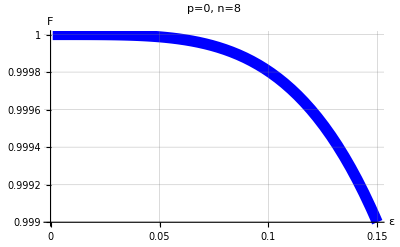

```mathematica
PFp08 = Plot[Fp0,{ε,0.001,0.15},PlotRange->{{0,0.15},{0.999,1}},PlotStyle->{Blue,Thickness[0.02]},GridLines->Automatic,Ticks->{{{0,"0"},{0.05,"0.05"},{0.1,"0.1"},{0.15,"0.15"}},{{0.999,"0.999"},{0.9992,"0.9992"},{0.9994,"0.9994"},{0.9996,"0.9996"},{0.9998,"0.9998"},{1,"1"}}},AxesStyle->Thick,PlotLabel->"p=0, n=8",AxesLabel->{"ε","F"}];
Show[PFp08]
```